```mathematica
xDataContent = Import["/Users/josephbarrow/Dropbox/hackathon/Boulder/data/x.data"]
```

```mathematica
xDataLabels = First[dataContent]
```

{X,TIME}

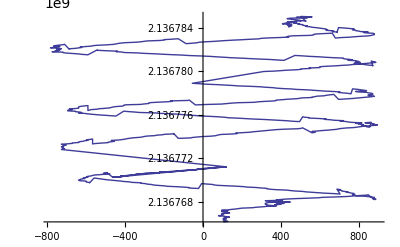

```mathematica
ListLinePlot[xDataPoints]
```

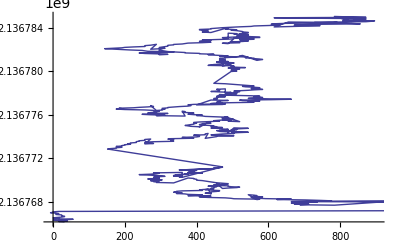

```mathematica
ListLinePlot[yDataPoints]
```

```mathematica
zDataContent = Import["/Users/josephbarrow/Dropbox/hackathon/Boulder/data/z.data"]
```

```mathematica
zDataPoints = Rest[zDataContent]
```

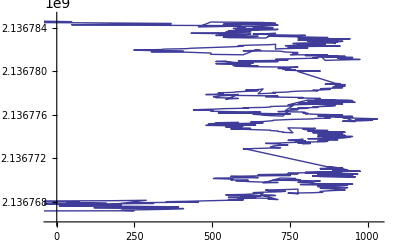

```mathematica
ListLinePlot[zDataPoints]
```

```mathematica
FFT[ListLinePlot[xDataPoints]]
```

```mathematica
Fourier[xDataPoints]
```

{{4.07671×10^10+0. ⅈ,-4.07671×10^10+0. ⅈ},{399.461-59852.2 ⅈ,1508.01+56748.5 ⅈ},«725»,{399.461+59852.2 ⅈ,1508.01-56748.5 ⅈ}}

```mathematica
ListPlot[Fourier[xDataPoints]]
```

ListPlot::lpn: {{{4.07671×10^10 + 0.\ ⅈ, -4.07671×10^10 + 0.\ ⅈ}, {399.461  - 59852.2\ ⅈ, 1508.01  + 56748.5\ ⅈ}, « 47 », {-166.225 - 1132.18\ ⅈ, 312.804  + 1039.41\ ⅈ}, « 678 »}} is not a list of numbers or pairs of numbers.

ListPlot[{{4.07671×10^10+0. ⅈ,-4.07671×10^10+0. ⅈ},{399.461-59852.2 ⅈ,1508.01+56748.5 ⅈ},«725»,{399.461+59852.2 ⅈ,1508.01-56748.5 ⅈ}}]

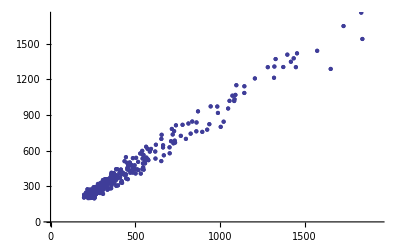

```mathematica
ListPlot[Sqrt[Abs[Fourier[xDataPoints]]^2]]
```